-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 1 I Thermodynamics

## I. A Fundamental Definitions

Thermodynamics provides a macroscopic description of the equilibrium properties of large-scale systems, focusing on observable phenomena rather than microscopic details.

```mathematica
(2) -- Thermodynamics is a phenomenological description, grounded in empirical observations encapsulated by its laws. These observations serve as the foundation for constructing a coherent logical and mathematical framework, introducing various useful concepts and testable relationships among quantities. However, the laws of thermodynamics find their justification in more fundamental microscopic theories of nature. Statistical mechanics, for instance, aims to derive these laws from the classical or quantum mechanical equations governing the evolution of particle ensembles.
```

(3) -- Equilibrium is a pivotal concept in the realm of thermodynamics and statistical mechanics. A system under investigation is deemed to be in equilibrium when its properties exhibit negligible variation over the time scales of interest (observation times). Notably, the dependence on the observation time renders the concept of equilibrium inherently subjective. For instance, window glass is considered a solid in equilibrium over decades, yet it exhibits fluid-like behavior over millennia. Conversely, it is perfectly valid to consider the equilibrium between matter and radiation during the initial minutes of the Big Bang, marking the early stages of the universe's evolution.

The macroscopic system in equilibrium is characterized by a set of thermodynamic coordinates or state functions. Prevalent examples of such coordinates include pressure, volume, temperature, internal energy, and entropy. These coordinates provide a comprehensive description of the system's macroscopic state, enabling the analysis and prediction of its behavior through the fundamental laws of thermodynamics and statistical mechanics.

```mathematica
(4) -- In the realm of thermodynamics and statistical mechanics, various systems exhibit distinct conjugate variables that govern their equilibrium states. These pairs of variables encompass mechanical coordinates such as pressure and volume for fluids, surface tension and area for films, tension and length for wires, and electric field and polarization for dielectrics.

A closed system is an idealized construct akin to a point particle in mechanics, where it is assumed to be entirely isolated by adiabatic walls, precluding any exchange of heat with its surroundings. In contrast, diathermic walls permit heat transfer in an open system.

Beyond the mechanical coordinates, the fundamental laws of thermodynamics necessitate the existence of additional equilibrium state functions, which will be explored in the forthcoming sections.
```

(5) -- The transitive nature of thermal equilibrium is captured by the zeroth law of thermodynamics. If two systems, A and B, are separately in thermal equilibrium with a third system, C, then A and B are also in thermal equilibrium with each other. This law allows the definition of temperature as a property shared by systems in thermal equilibrium.

```mathematica
(6) -- The zeroth law of thermodynamics states that if two systems, A and B, are individually in thermal equilibrium with a third system C, then they must also be in thermal equilibrium with each other. This principle establishes the existence of an empirical temperature scale and forms the basis for the concept of temperature. It allows for the comparison and measurement of temperatures across different systems, enabling the study of thermal phenomena and the development of thermodynamic principles.
```

```mathematica
(7) -- The zeroth law, despite its apparent simplicity, has the profound consequence of implying the existence of an empirical state function, the temperature Θ. This temperature Θ is a property shared by systems in thermal equilibrium, ensuring that all such systems attain the same temperature value. This fundamental principle paves the way for the quantitative study of heat transfer and the development of the laws of thermodynamics.
```

(8) -- Consider an equilibrium state where systems A, B, and C are described by the coordinate sets {A1, A2, ...}, {B1, B2, ...}, and {C1, C2, ...}, respectively. The equilibrium condition between A and C implies a constraint on their coordinates. A change in A1 necessitates adjustments in {A2, ...; C1, C2, ...} to maintain the equilibrium of A and C. Let this constraint be denoted by f(A1, A2, ...; C1, C2, ...) = 0. Similarly, the equilibrium between B and C imposes g(B1, B2, ...; C1, C2, ...) = 0.

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["f_{A C}\\left(A_{1}, A_{2}, \\cdots ; C_{1}, C_{2}, \\cdots\\right)=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f_{A C}\\left(A_{1}, A_{2}, \\cdots ; C_{1}, C_{2}, \\cdots\\right)=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_AC[A_1,A_2,⋯;C_1,C_2,⋯]==0

```mathematica
(10) -- The equilibrium of B and C implies a similar constraint
```

Statistical Mechanics
Ramirez (11)

```mathematica
MaTeX["f_{B C}\\left(B_{1}, B_{2}, \\cdots ; C_{1}, C_{2}, \\cdots\\right)=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f_{B C}\\left(B_{1}, B_{2}, \\cdots ; C_{1}, C_{2}, \\cdots\\right)=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_BC[B_1,B_2,⋯;C_1,C_2,⋯]==0

(12) -- Each of the above equations can be solved for C_1 to yield

Statistical Mechanics
Ramirez (13)

```mathematica
MaTeX["\\begin{aligned}& C_{1}=F_{A C}\\left(A_{1}, A_{2}, \\cdots ; C_{2}, \\cdots\\right) \\\\& C_{1}=F_{B C}\\left(B_{1}, B_{2}, \\cdots ; C_{2}, \\cdots\\right)\\end{aligned}", Magnification -> 4]
```

-Graphics-

(14) -- Thus if C is separately in equilibrium with A and B we must have

Statistical Mechanics
Ramirez (15)

```mathematica
MaTeX["F_{A C}\\left(A_{1}, A_{2}, \\cdots ; C_{2}, \\cdots\\right)=F_{B C}\\left(B_{1}, B_{2}, \\cdots ; C_{2}, \\cdots\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F_{A C}\\left(A_{1}, A_{2}, \\cdots ; C_{2}, \\cdots\\right)=F_{B C}\\left(B_{1}, B_{2}, \\cdots ; C_{2}, \\cdots\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F_AC[A_1,A_2,⋯;C_2,⋯]==F_BC[B_1,B_2,⋯;C_2,⋯]

```mathematica
(16) -- However, according to the zeroth law there is also equilibrium between A and B, implying the constraint
```

Statistical Mechanics
Ramirez (17)

```mathematica
MaTeX["f_{A B}\\left(A_{1}, A_{2}, \\cdots ; B_{1}, B_{2}, \\cdots\\right)=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f_{A B}\\left(A_{1}, A_{2}, \\cdots ; B_{1}, B_{2}, \\cdots\\right)=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_AB[A_1,A_2,⋯;B_1,B_2,⋯]==0

(18) -- The freedom to choose the coordinates of the constraint point C allows us to simplify equation (I.4) by eliminating the coordinates of C. Consequently, the equilibrium condition (I.5) for systems A and B can be expressed in a more concise form, preserving the underlying physical principles.

Statistical Mechanics
Ramirez (19)

```mathematica
MaTeX["\\Theta_{A}\\left(A_{1}, A_{2}, \\cdots\\right)=\\Theta_{B}\\left(B_{1}, B_{2}, \\cdots\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Theta_{A}\\left(A_{1}, A_{2}, \\cdots\\right)=\\Theta_{B}\\left(B_{1}, B_{2}, \\cdots\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Θ_A[A_1,A_2,⋯]==Θ_B[B_1,B_2,⋯]

(20) -- In the realm of thermodynamics and statistical mechanics, equilibrium states are characterized by a thermodynamic potential Θ, which is a function of thermodynamic coordinates. This potential encapsulates the equation of state, governing the relationships between various thermodynamic variables. For a specific thermodynamic quantity A, the isotherms, representing curves of constant A, are described by the condition Θ_A(A_1, A_2, ...) = Θ, where A_1, A_2, ... are the relevant thermodynamic coordinates. The thermodynamic potential Θ serves as a unifying framework, linking the macroscopic properties of a system to its underlying microscopic behavior, providing a comprehensive description of equilibrium states.

```mathematica
(21) -- In the realm of thermodynamics and statistical mechanics, we encounter three distinct systems: (A) a wire of length L subjected to tension F, (B) a paramagnetic material with magnetization M under the influence of a magnetic field B, and (C) a gaseous system with volume V and pressure P. Empirical observations reveal that when these systems attain equilibrium, their respective coordinates adhere to the following constraints:
```

Statistical Mechanics
Ramirez (22)

```mathematica
MaTeX["\\begin{gathered}\\left(P+\\frac{a}{V^{2}}\\right)(V-b)\\left(L-L_{0}\\right)-c\\left[F-K\\left(L-L_{0}\\right)\\right]=0 \\\\\\left(P+\\frac{a}{V^{2}}\\right)(V-b) M-d B=0\\end{gathered}", Magnification -> 4]
```

-Graphics-

```mathematica
(23) -- Clearly these constraints can be organized into three empirical temperature functions as
```

Statistical Mechanics
Ramirez (24)

```mathematica
MaTeX["\\Theta \\propto\\left(P+\\frac{a}{V^{2}}\\right)(V-b)=c\\left(\\frac{F}{L-L_{0}}-K\\right)=d \\frac{B}{M}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Theta \\propto\\left(P+\\frac{a}{V^{2}}\\right)(V-b)=c\\left(\\frac{F}{L-L_{0}}-K\\right)=d \\frac{B}{M}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(Θ∝(P+a/V^2) (V-b))==c[F/(L-L_0)-K]==(d B)/M

```mathematica
(25) -- These are the well known equations of state describing:
```

Statistical Mechanics
Ramirez (26)

```mathematica
MaTeX["\\left\\{\\begin{aligned}\\left(P+a / V^{2}\\right)(V-b)=N k_{B} T & \\text {(van der Waals gas)} \\\\M=\\left(N \\mu_{B}^{2} B\\right) /\\left(3 k_{B} T\\right) & \\text {(Curie paramagnet)} \\\\F=(K+D T)\\left(L-L_{0}\\right) & (\\text {Hook's law for rubber)}\\end{aligned}\\right.", Magnification -> 4]
```

-Graphics-

(27) -- The zeroth law establishes the existence of isotherms, which are surfaces of constant temperature. To construct a practical temperature scale, a reference system is required. The ideal gas serves as an essential reference in thermodynamics. Empirical observations reveal that for any sufficiently dilute gas, the product of pressure and volume remains constant along its isotherms. The ideal gas represents the dilute limit of real gases, and its temperature is proportional to the product PV. The constant of proportionality is determined by setting the temperature of the triple point of the ice-water-vapor system to 273.16 degrees Kelvin (°K), as established by the 10th General Conference on Weights and Measures in 1954. By utilizing a dilute gas (i.e., as P → 0) as a thermometer, the temperature of a system can be obtained from the proportionality relationship.

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["T\\left({}^{o} K\\right) \\equiv 273.16 \\times\\left(\\lim _{P \\rightarrow 0}(P V)_{\\text {system}} / \\lim _{P \\rightarrow 0}(P V)_{\\text {ice-water-gas}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["T\\left({}^{o} K\\right) \\equiv 273.16 \\times\\left(\\lim _{P \\rightarrow 0}(P V)_{\\text {system}} / \\lim _{P \\rightarrow 0}(P V)_{\\text {ice-water-gas}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

T[^o K]≡273.16 x[lim_(P→0) PV_system/(lim_(P→0) PV_(ice-water-gas))]

```mathematica
I.C The First law
```

We now consider transformations between different equilibrium states. Such transformations can be achieved by applying work or heat to the system. The first law states that both work and heat are forms of energy, and that the total energy is conserved. We shall use the following formulation:

```mathematica
(30) -- The principle of adiabatic invariance governs the work required to alter the state of an isolated system. Regardless of the intricacies involved, the work expended hinges solely upon the initial and terminal states, disregarding the intermediary steps or the specific means employed.
```

(31) -- The existence of a state function, the internal energy U, arises as a natural consequence of the first law of thermodynamics. This state function encompasses the total energy of a system, encompassing both the kinetic and potential energies of its constituent particles. The internal energy is a pivotal concept, as its differential form, dU, represents the amount of energy transferred to or from the system during an infinitesimal process, accounting for the work done by or on the system (δW) and the heat exchanged with its surroundings (δQ):

dU = δQ - δW

This fundamental relationship underscores the significance of the internal energy as a unifying principle, bridging the realms of thermodynamics and statistical mechanics, and enabling the quantitative analysis of energy transformations in various physical processes.

(32) -- The energy function, E(X), is a fundamental concept in thermodynamics and statistical mechanics. It represents the total energy associated with a particular configuration or state X of a system. The energy function can be determined, up to an additive constant, by considering the amount of work ΔW required for an adiabatic transformation from an initial state Xi to a final state Xf. This work is related to the change in the energy function through the following relation:

ΔW = E(Xf) - E(Xi)

In this expression, ΔW represents the work performed during the adiabatic process, which involves no exchange of heat with the surroundings. By evaluating the work required for such a transformation, one can obtain the difference in energy between the initial and final states, thereby providing a means to determine the energy function itself, up to an additive constant.

Statistical Mechanics
Ramirez (33)

```mathematica
MaTeX["\\Delta W=E\\left(\\mathbf{X}_{\\mathbf{f}}\\right)-E\\left(\\mathbf{X}_{\\mathbf{i}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Delta W=E\\left(\\mathbf{X}_{\\mathbf{f}}\\right)-E\\left(\\mathbf{X}_{\\mathbf{i}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Δ W==ⅇ[X_f]-ⅇ[X_i]

(34) -- In a generic transformation, where the system is not thermally insulated from its surroundings, the work done on or by the system does not equate to the change in its internal energy. The difference ΔQ = ΔE - ΔW is defined as the heat absorbed by the system from its environment. It is evident that in such transformations, ΔQ and ΔW are not state functions, as they depend on external factors like the manner in which work is applied, and not solely on the initial and final states. To emphasize this, for an infinitesimal transformation, we write:

dQ = dE - dW

The differential forms highlight that heat and work are not exact differentials, and their values depend on the specific path taken during the transformation.

Statistical Mechanics
Ramirez (35)

```mathematica
MaTeX["d Q=d E-d W", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d Q=d E-d W",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dQ==dE-dW

(36) -- where

```mathematica
MaTeX["d E=\sum_{i} \partial_{i} E d X_{i}"]
```

-Graphics-

(36)  can be obtained by differentiation, while $d Q$ and $d W$ generally can not. Also note the convention that the signs of work and heat are chosen to indicate the energy added to the system, and not vice versa.

(37) -- A transformation that occurs at an infinitesimally slow rate is known as a quasi-static process. In such a process, the system remains in equilibrium at every instant, allowing for the determination of its thermodynamic coordinates. For quasi-static transformations, the work performed on the system (or by the system, with opposite sign) can be related to changes in these coordinates. 

The state functions {X} can be divided into a set of generalized displacements {x} and their conjugate generalized forces {J}, such that for an infinitesimal quasi-static transformation:

δW = Σ J_i dx_i

Where δW represents the infinitesimal work done on the system during the quasi-static process, J_i are the generalized forces, and dx_i are the corresponding infinitesimal generalized displacements.

Statistical Mechanics
Ramirez (38)

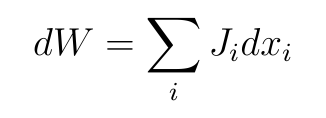

```mathematica
MaTeX["d W=\\sum_{i} J_{i} d x_{i}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["d W=\\sum_{i} J_{i} d x_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dW==∑_i J_i d x_i

```mathematica
(39) -- Table [1] illustrates typical examples of conjugate variables encountered in thermodynamic systems. The displacement coordinates are extensive quantities, scaling with the system size, whereas the force-like variables are intensive, independent of the system's dimensions. Notably, the pressure is conventionally calculated from the force exerted by the system on its confining walls, in contrast to the force exerted on a spring, which acts in the opposite direction. This convention introduces a negative sign in the expression for the hydrostatic work term.
```

(40) -- The table illustrates the conjugate pairs of thermodynamic variables associated with different systems. In thermodynamics, work is defined as the product of a generalized force and its corresponding displacement or generalized coordinate.

For a wire, the force is tension, and the displacement is its length change. In the case of a film, the force is surface tension, and the displacement is the change in surface area. For fluids, the force is pressure, and the displacement is the volume change.

In magnetism, the force is the magnetic field, and the displacement is the magnetization (M). For dielectric materials, the force is the electric field, and the displacement is the polarization.

In chemical reactions, the force is the chemical potential (μ), and the displacement is the change in the number of particles (N).

These conjugate pairs form the basis for calculating the work done on or by a system during a thermodynamic process, which is a fundamental concept in the study of energy transformations and the behavior of systems at the microscopic level.

(41) -- Table 1: Generalized Forces and Displacements

```mathematica
(42) -- Joule's Free Expansion Experiment: The internal energy of an ideal gas remains unchanged during an adiabatic free expansion process, where the gas expands from an initial volume V_i to a final volume V_f without any heat transfer or external work. This observation implies that the internal energy of an ideal gas is solely a function of temperature, E(V, T) = E(T).

The adiabatic free expansion transformation occurs with ΔQ = 0 (no heat transfer) and ΔW = 0 (no external work). Since the internal energy change ΔU = ΔQ + ΔW, the internal energy remains constant during the process. However, the pressure and volume of the gas change, while the temperature remains unchanged.

This property of the ideal gas, where the internal energy depends only on temperature, is a direct consequence of its equation of state, which will be derived in the subsequent review problems.
```

```mathematica
(43) -- Response functions characterize the macroscopic behavior of a system by quantifying the changes in thermodynamic coordinates induced by external probes. These experimentally measured quantities provide valuable insights into the system's properties. Some common response functions include:

1. Isothermal compressibility (κ_T): κ_T = -(1/V)(∂V/∂P)_T, which measures the volume change with respect to pressure at constant temperature.

2. Isobaric heat capacity (C_P): C_P = (∂Q/∂T)_P, quantifying the heat required to raise the temperature at constant pressure.

3. Isothermal magnetic susceptibility (χ_T): χ_T = (∂M/∂H)_T, describing the magnetization response to an applied magnetic field at constant temperature.

4. Isothermal dielectric susceptibility (ε_T): ε_T = (∂P/∂E)_T, characterizing the polarization induced by an electric field at constant temperature.

These response functions provide crucial information about the system's thermodynamic stability, phase transitions, and underlying microscopic interactions, making them invaluable tools in the study of thermodynamics and statistical mechanics.
```

```mathematica
(44) -- Heat capacities quantify the amount of heat required to raise the temperature of a system by a certain amount. They are obtained by measuring the change in temperature upon addition of heat to the system. Since heat is a path function, the process by which it is supplied must be specified. For gases, we distinguish between the heat capacity at constant volume, CV = dQ/dT|V, and the heat capacity at constant pressure, CP = dQ/dT|P. The latter is larger because some of the heat supplied is utilized in performing work against the surroundings as the gas expands.
```

Statistical Mechanics
Ramirez (45)

```mathematica
MaTeX["\\begin{aligned}& C_{V}=\\left.\\frac{d Q}{d T}\\right|_{V}=\\left.\\frac{d E-d W}{d T}\\right|_{V}=\\left.\\frac{d E+P d V}{d T}\\right|_{V}=\\left.\\frac{\\partial E}{\\partial T}\\right|_{V} \\\\& C_{P}=\\left.\\frac{d Q}{d T}\\right|_{P}=\\left.\\frac{d E-d W}{d T}\\right|_{P}=\\left.\\frac{d E+P d V}{d T}\\right|_{P}=\\left.\\frac{\\partial E}{\\partial T}\\right|_{P}+\\left.P \\frac{\\partial V}{\\partial T}\\right|_{P}\\end{aligned}", Magnification -> 4]
```

-Graphics-

(46) -- Force Constants quantify the relationship between infinitesimal displacements and the corresponding forces. They generalize the concept of a spring constant. The isothermal compressibility of a gas κ_T=-∂V/∂P|_T/V and the magnetic susceptibility χ_T=∂M/∂B|_T/V are examples of Force Constants. For an ideal gas, with the equation of state PV ∝ T, the isothermal compressibility is κ_T=1/P.

(47) -- Thermal Responses probe the change in the thermodynamic coordinates with temperature.

```mathematica
(48) -- The expansivity of a gas, denoted by αP, quantifies the change in volume V with respect to temperature T at constant pressure P. It is expressed as αP = (∂V/∂T)P / V. For an ideal gas, this quantity simplifies to 1/T, indicating that the volume of an ideal gas increases linearly with temperature when the pressure is held constant.
```

```mathematica
(49) -- The internal energy of an ideal gas is solely a function of its temperature. Consequently, the partial derivatives of internal energy with respect to temperature at constant volume and constant pressure are equivalent to the total derivative of internal energy with respect to temperature, expressed as ∂E/∂T|V = ∂E/∂T|P = dE/dT. This simplification allows us to rewrite equation (I.14) in a more concise form.
```

Statistical Mechanics
Ramirez (50)

```mathematica
MaTeX["C_{P}-C_{V}=\\left.P \\frac{\\partial V}{\\partial T}\\right|_{P}=P V \\alpha_{P}=\\frac{P V}{T} \\equiv N k_{B}", Magnification -> 4]
```

-Graphics-

(51) -- The thermodynamic quantity PV/T, where P is the pressure, V is the volume, and T is the absolute temperature, is an extensive property for an ideal gas. This means that for a given amount of ideal gas, PV/T is directly proportional to the number of particles, N, present in the gas. The constant of proportionality is known as the Boltzmann constant, kB, which has a value of approximately 1.4 × 10^-23 J/K. This fundamental relation underpins the statistical mechanical description of ideal gases and is a cornerstone of the kinetic theory of gases.

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear